Let us start by drawing a picture. We are trying to find a lower bound on the angle between m⃗ and n⃗ (for q between 0 and 1 and χ between 0 and π/2) which is the same as the red angle depicted below.

```mathematica
Manipulate[
Module[{X,c,t,n,δ,ϵ,T,z,k},
X={√(q+q^2)Sin[χ],q Cos[χ]};
If[χ==0,c={-(√(-q (-16-4 q+4 q^2+q^3)))/(2 (1+q)),(2+q^2)/(2+2 q)},c={(Csc[χ] (16 q+19 q^2+7 q^3+4 q^4-4 q (4+5 q+2 q^2+q^3) Cos[2 χ]-4 q^2 Cos[3 χ]-4 q^3 Cos[3 χ]+q^2 Cos[4 χ]+q^3 Cos[4 χ]-2 √2 √(-q^2 (1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]) Sin[χ]^2)+Cos[χ] (4 q^2+4 q^3-2 √2 q √(-q^2 (1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]) Sin[χ]^2))))/(8 √(q (1+q)) (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ])),(8-2 q+8 q Cos[χ]+q^2 Cos[χ]+4 q^3 Cos[χ]+2 q Cos[2 χ]+4 q^2 Cos[2 χ]-q^2 Cos[3 χ]+√2 √(-q^2 (1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]) Sin[χ]^2))/(4 (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]))}];
t=Normalize[{√(q+q^2)Cos[χ],-q Sin[χ]}];
n=Normalize[{q Sin[χ],√(q+q^2)Cos[χ]}];
{δ,ϵ}={ArcTan@@(c-X),ArcTan@@(-n)};
If[δ<0,δ=δ+2π];
If[ϵ<0,ϵ=ϵ+2π];
T={1/(2 a (a^2+(1+b)^2))(a^4+a^2 (2 b+b^2+(1+q)^2)+(1+b)a√(-(a^4+4 b^3+b^4-4 b (1+q)^2+(1+q)^2 (-3+2 q+q^2)-2 b^2 (-1+2 q+q^2)+2 a^2 (2 b+b^2-(1+q)^2)))),1/(2 (a^2+(1+b)^2))(-1-a^2-b+a^2 b+b^2+b^3+2 q+2 b q+q^2+b q^2-a√(-(a^4+4 b^3+b^4-4 b (1+q)^2+(1+q)^2 (-3+2 q+q^2)-2 b^2 (-1+2 q+q^2)+2 a^2 (2 b+b^2-(1+q)^2))))}/.{a->c⟦1⟧,b->c⟦2⟧};
{z,k}={ArcTan@@(c-T),ArcTan@@({0,-1}-T)};
If[z<0,z=z+2π];
If[k<0,k=k+2π];
Graphics[{
{Gray,Circle[{0,-1},1],Circle[c,1]},
{Blue,Circle[{0,0},{√(q+q^2),q}],AbsolutePointSize[5],Point[{0,0}],Text[Style["S",Italic,Bold],{0,-0.1}]},
{Red,Line[{X-2n,X,X+2(c-X)}],Circle[X,0.3,{δ,ϵ}],Line[{{2.3,1},{3.3,1},{3.3,1}+{-Cos[ϵ-δ],Sin[ϵ-δ]}}],AbsolutePointSize[5],Point[X],Text[Style["X",Italic,Bold],X+{0.05,0.08}],Circle[{3.3,1},0.3,{π-(ϵ-δ),π}],Dotted,Line[{X-t,X+t}]},
{RGBColor[0.4,0,1],Arrow[{X,X+n}],Text[Style["n⃗",Italic,Bold],X+n/2],Arrow[{X,2X-c}],Text[Style["m⃗",Italic,Bold],(3X-c)/2]},
{Text[ϵ-δ,{2.8,0.8}]}
},AspectRatio->Automatic,PlotRange->{{-2,3.5},{-2,2}},ImageSize->Large]
],
{{q,1},0,1,Appearance->"Open"},{{χ,1.4},0,π/2,Appearance->"Open"}]
```

We compute the center of the τ-ball which has X (determined by q and χ) on its boundary and which touches the drawn τ-ball, associated to S.

```mathematica
Simplify[Solve[x^2+(y+1)^2==4∧(x-√(q+q^2)Sin[χ])^2+(y-q Cos[χ])^2==1,{x,y}],0<q<1∧0≤χ≤π/2]
```

{{x→-1/(4 √(q (1+q)) (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]))q (√2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))+√2 q Cos[χ] √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-16 Sin[χ]-19 q Sin[χ]-7 q^2 Sin[χ]-4 q^3 Sin[χ]-4 q Sin[2 χ]-4 q^2 Sin[2 χ]+q Sin[3 χ]+q^2 Sin[3 χ]),y→(8-2 q+8 q Cos[χ]+q^2 Cos[χ]+4 q^3 Cos[χ]+2 q Cos[2 χ]+4 q^2 Cos[2 χ]-q^2 Cos[3 χ]+√2 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ])/(4 (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]))},{x→1/(4 √(q (1+q)) (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]))q (√2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))+√2 q Cos[χ] √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))+16 Sin[χ]+19 q Sin[χ]+7 q^2 Sin[χ]+4 q^3 Sin[χ]+4 q Sin[2 χ]+4 q^2 Sin[2 χ]-q Sin[3 χ]-q^2 Sin[3 χ]),y→(8-2 q+8 q Cos[χ]+q^2 Cos[χ]+4 q^3 Cos[χ]+2 q Cos[2 χ]+4 q^2 Cos[2 χ]-q^2 Cos[3 χ]-√2 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ])/(4 (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]))}}

The intersection we want is the one with the larger x-coordinate. We store this value into the variable center. From this we calculate the cotangent of both rays of the red angle. Using the addition theorem for cotangent, we obtain the cotangent of the red angle itself.

```mathematica
Module[{center,X,n,CX,ct1,ct2},
center={-((q (√2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))+√2 q Cos[χ] √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-16 Sin[χ]-19 q Sin[χ]-7 q^2 Sin[χ]-4 q^3 Sin[χ]-4 q Sin[2 χ]-4 q^2 Sin[2 χ]+q Sin[3 χ]+q^2 Sin[3 χ]))/(4 √(q (1+q)) (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]))),1/(4 (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]))(8-2 q+8 q Cos[χ]+q^2 Cos[χ]+4 q^3 Cos[χ]+2 q Cos[2 χ]+4 q^2 Cos[2 χ]-q^2 Cos[3 χ]+√2 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ])};
X={√(q+q^2)Sin[χ],q Cos[χ]};
n={q Sin[χ],√(q+q^2)Cos[χ]};
CX=center-X;
ct1=CX⟦1⟧/CX⟦2⟧;
ct2=n⟦1⟧/n⟦2⟧;
Simplify[(ct1 ct2+1)/(ct1-ct2),0<q<1∧0≤χ≤π/2]
]
```

(-2 (-8-7 q+13 q^2+12 q^3) Cos[χ]+q (8+4 q-12 q^2-8 q^3-8 Cos[2 χ]-4 q Cos[2 χ]+4 q^2 Cos[2 χ]+2 Cos[3 χ]+2 q Cos[3 χ]-2 √2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ]+√2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[2 χ]))/(√(q (1+q)) (-2 √2 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-2 √2 Cos[χ] √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-16 Sin[χ]+2 q Sin[χ]+8 q^2 Sin[χ]+8 Sin[2 χ]+6 q Sin[2 χ]-4 q^2 Sin[2 χ]-6 q Sin[3 χ]+q Sin[4 χ]))

We define the function ct, which measures the cotangent of the red angle.

```mathematica
ct[q_,χ_]:=(-2 (-8-7 q+13 q^2+12 q^3) Cos[χ]+q (8+4 q-12 q^2-8 q^3-8 Cos[2 χ]-4 q Cos[2 χ]+4 q^2 Cos[2 χ]+2 Cos[3 χ]+2 q Cos[3 χ]-2 √2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ]+√2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[2 χ]))/(√(q (1+q)) (-2 √2 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-2 √2 Cos[χ] √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-16 Sin[χ]+2 q Sin[χ]+8 q^2 Sin[χ]+8 Sin[2 χ]+6 q Sin[2 χ]-4 q^2 Sin[2 χ]-6 q Sin[3 χ]+q Sin[4 χ]));
```

We claim that ct is increasing in q for every χ.

```mathematica
Manipulate[
Plot[ct[q,χ],{q,0,1},AspectRatio->Automatic,PlotRange->{{0,1},{-1,1}}],
{{χ,1.2},0,π/2,Appearance->"Open"}]
```

To verify this, we prove that the partial derivative of ct with respect to q, which we denote by dct, is ≥0.

```mathematica
Simplify[Together[D[ct[q,χ],q]],0<q<1∧0≤χ≤π/2]
```

(4 (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]) (16 √2+258 √2 q+586 √2 q^2+424 √2 q^3+144 √2 q^4+64 √2 q^5+192 √2 Cos[χ]+464 √2 q Cos[χ]+448 √2 q^2 Cos[χ]+368 √2 q^3 Cos[χ]+192 √2 q^4 Cos[χ]+127 √2 q Cos[2 χ]+175 √2 q^2 Cos[2 χ]+32 √2 q^3 Cos[2 χ]-16 √2 q^4 Cos[2 χ]+64 √2 Cos[3 χ]+56 √2 q Cos[3 χ]+8 √2 q^2 Cos[3 χ]+16 √2 q^3 Cos[3 χ]-16 √2 Cos[4 χ]-2 √2 q Cos[4 χ]+6 √2 q^2 Cos[4 χ]-8 √2 q^3 Cos[4 χ]-8 √2 q Cos[5 χ]-8 √2 q^2 Cos[5 χ]+√2 q Cos[6 χ]+√2 q^2 Cos[6 χ]-4 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ]-16 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ]-32 q^2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ]+8 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[2 χ]+8 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[2 χ]+16 q^2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[2 χ]-4 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[3 χ]))/(q (1+q) √(-q (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) (-2 √2 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-2 √2 Cos[χ] √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-16 Sin[χ]+2 q Sin[χ]+8 q^2 Sin[χ]+8 Sin[2 χ]+6 q Sin[2 χ]-4 q^2 Sin[2 χ]-6 q Sin[3 χ]+q Sin[4 χ])^2)

```mathematica
dct[q_,χ_]:=(4 (2+q+2 q^2+4 q Cos[χ]-q Cos[2 χ]) (16 √2+258 √2 q+586 √2 q^2+424 √2 q^3+144 √2 q^4+64 √2 q^5+192 √2 Cos[χ]+464 √2 q Cos[χ]+448 √2 q^2 Cos[χ]+368 √2 q^3 Cos[χ]+192 √2 q^4 Cos[χ]+127 √2 q Cos[2 χ]+175 √2 q^2 Cos[2 χ]+32 √2 q^3 Cos[2 χ]-16 √2 q^4 Cos[2 χ]+64 √2 Cos[3 χ]+56 √2 q Cos[3 χ]+8 √2 q^2 Cos[3 χ]+16 √2 q^3 Cos[3 χ]-16 √2 Cos[4 χ]-2 √2 q Cos[4 χ]+6 √2 q^2 Cos[4 χ]-8 √2 q^3 Cos[4 χ]-8 √2 q Cos[5 χ]-8 √2 q^2 Cos[5 χ]+√2 q Cos[6 χ]+√2 q^2 Cos[6 χ]-4 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ]-16 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ]-32 q^2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[χ]+8 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[2 χ]+8 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[2 χ]+16 q^2 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[2 χ]-4 √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) Sin[3 χ]))/(q (1+q) √(-q (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ])) (-2 √2 q √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-2 √2 Cos[χ] √(-(1+q) (-32-45 q+8 q^2+8 q^3+8 (-16+q+4 q^2) Cos[χ]+(32+12 q-8 q^2) Cos[2 χ]-8 q Cos[3 χ]+q Cos[4 χ]))-16 Sin[χ]+2 q Sin[χ]+8 q^2 Sin[χ]+8 Sin[2 χ]+6 q Sin[2 χ]-4 q^2 Sin[2 χ]-6 q Sin[3 χ]+q Sin[4 χ])^2);
```

```mathematica
Plot3D[{0,dct[q,χ]},{q,0,1},{χ,0,π/2},ClippingStyle->None]
```

-Graphics3D-

```mathematica
Manipulate[
Plot[dct[q,χ],{q,0,1},AspectRatio->Automatic,PlotRange->{{0,1},{0,3}}],
{{χ,1.2},0,π/2,Appearance->"Open"}]
```

Since ct is increasing in the first variable, it follows that any upper bound of ct[1, _ ] will also be an upper bound for the whole ct.

```mathematica
Simplify[ct[1,χ],0≤χ≤π/2]
```

(Sec[χ/2] (4+10 Cos[χ]+4 Cos[2 χ]-2 Cos[3 χ]+2 √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ]) Sin[χ]-√(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ]) Sin[2 χ]))/(4 √2 (Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+2 (1-4 Cos[χ]+Cos[2 χ]) Sin[χ/2]^3))

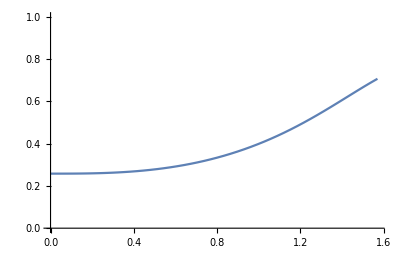

```mathematica
Plot[ct[1,χ],{χ,0,π/2},AspectRatio->Automatic,PlotRange->{{0,π/2},{0,1}}]
```

This is also an increasing function; let us verify that its derivative is positive.

```mathematica
Simplify[D[(Sec[χ/2] (4+10 Cos[χ]+4 Cos[2 χ]-2 Cos[3 χ]+2 √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ]) Sin[χ]-√(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ]) Sin[2 χ]))/(4 √2 (Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+2 (1-4 Cos[χ]+Cos[2 χ]) Sin[χ/2]^3)),χ],0≤χ≤π/2]
```

-((2 √2 (-5 Cos[χ/2]+Cos[(3 χ)/2]) Sin[χ/2]^2 (20 Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+4 Cos[(3 χ)/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])-102 Sin[χ/2]-12 Sin[(3 χ)/2]-12 Sin[(5 χ)/2]-5 Sin[(7 χ)/2]+Sin[(9 χ)/2]))/(√(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ]) (Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+2 (1-4 Cos[χ]+Cos[2 χ]) Sin[χ/2]^3)^2))

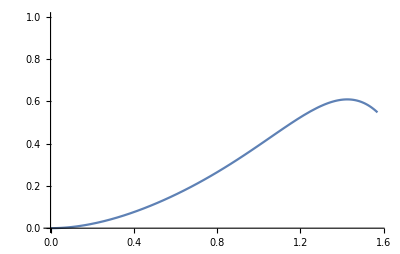

```mathematica
Plot[-((2 √2 (-5 Cos[χ/2]+Cos[(3 χ)/2]) Sin[χ/2]^2 (20 Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+4 Cos[(3 χ)/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])-102 Sin[χ/2]-12 Sin[(3 χ)/2]-12 Sin[(5 χ)/2]-5 Sin[(7 χ)/2]+Sin[(9 χ)/2]))/(√(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ]) (Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+2 (1-4 Cos[χ]+Cos[2 χ]) Sin[χ/2]^3)^2)),{χ,0,π/2},AspectRatio->Automatic,PlotRange->{{0,π/2},{0,1}}]
```

The denominator is clearly positive. Let us examine the numerator.

```mathematica
Numerator[-((2 √2 (-5 Cos[χ/2]+Cos[(3 χ)/2]) Sin[χ/2]^2 (20 Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+4 Cos[(3 χ)/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])-102 Sin[χ/2]-12 Sin[(3 χ)/2]-12 Sin[(5 χ)/2]-5 Sin[(7 χ)/2]+Sin[(9 χ)/2]))/(√(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ]) (Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+2 (1-4 Cos[χ]+Cos[2 χ]) Sin[χ/2]^3)^2))]
```

-2 √2 (-5 Cos[χ/2]+Cos[(3 χ)/2]) Sin[χ/2]^2 (20 Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])+4 Cos[(3 χ)/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])-102 Sin[χ/2]-12 Sin[(3 χ)/2]-12 Sin[(5 χ)/2]-5 Sin[(7 χ)/2]+Sin[(9 χ)/2])

The first part of the numerator is positive, as the following shows.

-2 √2 (-5 Cos[χ/2]+Cos[(3 χ)/2]) Sin[χ/2]^2 
==
2 √2 (5 Cos[χ/2]-(4 Cos[χ/2]^3-3Cos[χ/2]))Sin[χ/2]^2 
==
8 √2 Cos[χ/2](2-Cos[χ/2]^2)Sin[χ/2]^2

We can simplify the final factor as follows.

20 Cos[χ/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])
+4 Cos[(3 χ)/2] √(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])
-102 Sin[χ/2]-12 Sin[(3 χ)/2]-12 Sin[(5 χ)/2]-5 Sin[(7 χ)/2]+Sin[(9 χ)/2]
==
(20 Cos[χ/2]+4(4 Cos[χ/2]^3-3Cos[χ/2]))√(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])
-102 Sin[χ/2]-12 Sin[(3 χ)/2]-12 Sin[(5 χ)/2]-5 Sin[(7 χ)/2]+Sin[(9 χ)/2]
==
8Cos[χ/2](1+2 Cos[χ/2]^2)√(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ])
-102 Sin[χ/2]-12 Sin[(3 χ)/2]-12 Sin[(5 χ)/2]-5 Sin[(7 χ)/2]+Sin[(9 χ)/2]

The first line is clearly positive. If the second line is also positive, the total is positive. Otherwise, the positivity of this expression is equivalent to the positivity of the difference of the square of the first line and the square of the second line.

```mathematica
Simplify[(8Cos[χ/2](1+2 Cos[χ/2]^2)√(61+88 Cos[χ]-36 Cos[2 χ]+8 Cos[3 χ]-Cos[4 χ]))^2-(-102 Sin[χ/2]-12 Sin[(3 χ)/2]-12 Sin[(5 χ)/2]-5 Sin[(7 χ)/2]+Sin[(9 χ)/2])^2,0≤χ≤π/2]
```

18241+37815 Cos[χ]+11096 Cos[2 χ]+1290 Cos[3 χ]+580 Cos[4 χ]+66 Cos[5 χ]+40 Cos[6 χ]-7/2 Cos[7 χ]-5 Cos[8 χ]+1/2 Cos[9 χ]

This is positive, as the following shows.

18241+37815 Cos[χ]+11096 Cos[2 χ]+1290 Cos[3 χ]+580 Cos[4 χ]+66 Cos[5 χ]+40 Cos[6 χ]-7/2 Cos[7 χ]-5 Cos[8 χ]+1/2 Cos[9 χ]
≥
18241-11096-1290-580-66-40-7/2-5-1/2

```mathematica
18241-11096-1290-580-66-40-7/2-5-1/2
```

5160

Hence the maximum of ct is

```mathematica
ct[1,π/2]
```

1/(√2)

Since the red angle (the cotangent of which is ct) is between 0 and π, it follows that it is ≥ ArcCot[1/(√2)]. This is therefore also true for the angle between m⃗ and n⃗ which is what we are interested in.

The angle α_S X is 0 if pr(X)-X points inside the ellipsoid E_p(S), otherwise it is complementary to the angle between m⃗ and n⃗. Either way 0≤α_S X≤ArcTan[1/(√2)]. Equivalently, 0≤α_S X≤ArcCos[√(2/3)]; in particular Cos[α_S X]≥√(2/3).

```mathematica
Cos[ArcTan[1/(√2)]]
```

√(2/3)